```mathematica
SetDirectory["N:\\0MPX\\num200\\num200B"];
```

```mathematica
(*----------------------------RUN ALL ----------------------------*)
<<param\\paramCertain; (* certain param *)
<<param\\paramUncert;    (* matrix with sets of values for uncert param *)
 
Tmax=91;            (* #days to run *)
nsim=nmaxsim;  (* #param sets *)

(* initial conditions *) 
SUini=State0[[1]]; EUini=State0[[2]]; IUini=State0[[3]];YUini=State0[[4]];
SVini=State0[[5]]; EVini=State0[[6]]; IVini=State0[[7]];YVini=State0[[8]];
SPini=State0[[9]]; EPini=State0[[10]]; IPini=State0[[11]];YPini=State0[[12]];
RRini=State0[[13]]; HHini=State0[[14]]; 

(* total size of popul & infectious pop *)
Ntot[i_,t_]:=SU[i][t]+EU[i][t]+IU[i][t]+YU[i][t]+SV[i][t]+EV[i][t]+IV[i][t]+YV[i][t]+SP[i][t]+EP[i][t]+IP[i][t]+YP[i][t]+RR[i][t]+HH[i][t]; (*group i *)
Ntot[t_]:=Sum[Ntot[i,t],{i,1,ag}];    (* tot pop *)
Itot[t_]:=Sum[IU[i][t]+IV[i][t]+IP[i][t],{i,1,ag}];    (* total INFECTIOUS not-isolated *)
Ytot[t_]:=Sum[YU[i][t]+YV[i][t]+YP[i][t],{i,1,ag}];   (* total INFECTIOUS isolated *)
```

```mathematica
(*--------- VACCINATION BEFORE 25JULY2022 (CONTACTS OF CASES) ------------------*)
phi1d    =Izero;  (* vaccination of uninfected *)
phi2d    =Izero; (* vaccination of exposed *)
XTvac[t_]:=Piecewise[{{0,  t<42}, (* first 4w  *)
                                               {vacRate1,42≤t   }    }]
```

```mathematica
(************* LOOP ************)
Do[ (* START of loop of runs for each param set *)
infectiousDays=upAll[j,2];  
Tisol1                  =upAll[j,12];delta=1/Tisol1;gamma=1/(infectiousDays-Tisol1);  

theta=1/upAll[j,1];
betaS      =upAll[j,3];
aC4          =upAll[j,4];aC={aCd[[1]],aCd[[2]],aCd[[3]],aC4};
w               =upAll[j,5];
epsilonM=upAll[j,6];
epsilonC=upAll[j,7];
vacRate1=upAll[j,8];phi1={0,0,XTvac[t],XTvac[t]}; phi2=phi1;
v1             =upAll[j,9];sigma1=v1;sigma1HAT=v1;(* oldVE *)
v2             =upAll[j,10];sigma2=v2; (*newVE *)
zeta         =upAll[j,11];


(* parameters for transm prob with sex partners *) 
Bs[k_,l_]  :=(1-        betaS)^((uM[[k]]+uM[[l]])/2);(* sex contacts with main partn *)
Bsv[k_,l_]:=(1-v1*betaS)^((uM[[k]]+uM[[l]])/2);
Bsp[k_,l_]:=(1-v2*betaS)^((uM[[k]]+uM[[l]])/2);

(* mixing *)
mM[i_,l_,t_]:=epsilonM*dd[i][[l]]+(1-epsilonM)*aM[[l]]*Ntot[l,t]/Sum[aM[[jp]]*Ntot[jp,t],{jp,1,ag}];
mC[i_,l_,t_]:=epsilonC*dd[i][[l]]+(1-epsilonC)*aC[[l]]*Ntot[l,t]/Sum[aC[[jp]]*Ntot[jp,t],{jp,1,ag}];

(* LAMBDA'S *)
lambdaM[i_,t_ ]:=q[[i]]*Sum[ mM[i,l,t]*((1-Bs[i,l])*(IU[l][t]+w*YU[l][t])+(1-Bsv[i,l])*(IV[l][t]+w*YV[l][t])+(1-Bsp[i,l])*(IP[l][t]+w*YP[l][t]))/Ntot[l,t],{l,1,ag}];
lambdaC[i_,t_ ]:=aC[[i]]*betaS*Sum[ mC[i,l,t]*((IU[l][t]+w*YU[l][t])+v1*(IV[l][t]+w*YV[l][t])+v2*(IP[l][t]+w*YP[l][t]))/Ntot[l,t],{l,1,ag}];
lambda[i_,t_ ]     :=lambdaM[i,t ]+lambdaC[i,t ];

(* SOLVE  *)
xequa=Join[
Table[SU[i]'[t]  ==-(mu+lambda[i,t]+phi1[[i]])*SU[i][t]+mu*Ntot[i,t],{i,ag}],
Table[EU[i]'[t]==-(mu+phi2[[i]]+theta)*EU[i][t]+lambda[i,t]*SU[i][t],{i,ag}],
Table[IU[i]'[t]==-(mu+mud+delta+zeta)*IU[i][t]+theta*EU[i][t],{i,ag}],
Table[YU[i]'[t]==-(mu+mud+gamma+zeta)*YU[i][t]+delta*IU[i][t],{i,ag}],
Table[SV[i]'[t]==-(mu+sigma1*lambda[i,t]+phi1[[i]])*SV[i][t],{i,ag}],
Table[EV[i]'[t]==sigma1HAT*lambda[i,t]*SV[i][t]-(mu+theta+phi2[[i]])*EV[i][t],{i,ag}],
Table[IV[i]'[t]==sigma1*theta*EV[i][t]-(mu+mud+delta+zeta)*IV[i][t],{i,ag}],
Table[YV[i]'[t]==delta*IV[i][t]-(mu+mud+gamma+zeta)*YV[i][t],{i,ag}],
Table[SP[i]'[t]==phi1[[i]]*(SU[i][t]+SV[i][t])-(mu+sigma2*lambda[i,t])*SP[i][t],{i,ag}],
Table[EP[i]'[t]==sigma2*lambda[i,t]*SP[i][t]+phi2[[i]]*(EU[i][t]+EV[i][t])-(mu+theta)*EP[i][t],{i,ag}],
Table[IP[i]'[t]==sigma2*theta*EP[i][t]-(mu+delta)*IP[i][t],{i,ag}],
Table[YP[i]'[t]==delta*IP[i][t]-(mu+gamma)*YP[i][t],{i,ag}],
Table[RR[i]'[t]  ==-mu*RR[i][t]+(1-sigma1)*theta*EV[i][t]+(1-sigma2)*theta*EP[i][t]+gamma*(Ytot[t]+HH[i][t]),{i,ag}],
Table[HH[i]'[t]  ==-(mu+mud+gamma)*HH[i][t]+zeta*(IU[i][t]+YU[i][t]+IV[i][t]+YV[i][t]),{i,ag}],


Table[SU[i][0]==SUini[[i]],{i,ag}],
Table[EU[i][0]==EUini[[i]],{i,ag}],
Table[IU[i][0]==IUini[[i]],{i,ag}],
Table[YU[i][0]==YUini[[i]],{i,ag}],
Table[SV[i][0]==SVini[[i]],{i,ag}],
Table[EV[i][0]==EVini[[i]],{i,ag}],
Table[IV[i][0]==IVini[[i]],{i,ag}],
Table[YV[i][0]==YVini[[i]],{i,ag}],
Table[SP[i][0]==SPini[[i]],{i,ag}],
Table[EP[i][0]==EPini[[i]],{i,ag}],
Table[IP[i][0]==IPini[[i]],{i,ag}],
Table[YP[i][0]==YPini[[i]],{i,ag}],
Table[RR[i][0]==RRini[[i]],{i,ag}],
Table[HH[i][0]==HHini[[i]],{i,ag}]           ];
xvar=Join[Flatten[Table[{SU[i],EU[i],IU[i],YU[i],SV[i],EV[i],IV[i],YV[i],SP[i],EP[i],IP[i],YP[i],RR[i],HH[i]},{i,ag}]] ];
xresult=NDSolve[xequa,xvar,{t,0,Tmax},MaxSteps->50000];  

(* NUMBER developing symptoms (becoming infectious)/100,000MSM/d -- to be compared with #cases *)
nSympFUN[t_]:= Sum[theta*(EU[i][t]+sigma1*EV[i][t]+sigma2*EP[i][t]),{i,1,ag}];nSympEle[j]=(nSympFUN[t]/.xresult)[[1]];

If[Mod[j,200]==0 ,Print[j]],
 {j,1,nsim}];(* END of loop of runs for each param set *)
```

200

400

600

800

1000

1200

1400

1600

1800

2000

2200

2400

2600

2800

3000

3200

3400

3600

3800

4000

4200

4400

4600

4800

5000

5200

5400

5600

5800

6000

6200

6400

6600

6800

7000

7200

7400

7600

7800

8000

8200

8400

8600

8800

9000

9200

9400

9600

9800

10000

```mathematica
(*----- time points ------*)
tpoint=Table[it,{it,0,Tmax,1}];ntpoints=Length[tpoint];

(*----- save number daily cases --------*)
nSympMat  =Array[nSymp,{ntpoints}];
Do[t=tpoint[[it]];
nSymp[it]=Table[Evaluate[nSympEle[js]],{js,nsim}];
cumSymp[it]=Sum[nSymp[kk],{kk,1,it}];
,{it,1,ntpoints}];
```

```mathematica
(**********************************************)
Save["param\\NSympALLinitialParam",  {nSympMat,Tmax}];
(**********************************************)
```

```mathematica
(*----------- IMPORT DATA TO FIT  -------------------*)
dataAll=Flatten[Import["CasesPerOnsetDate.xls"]];
```

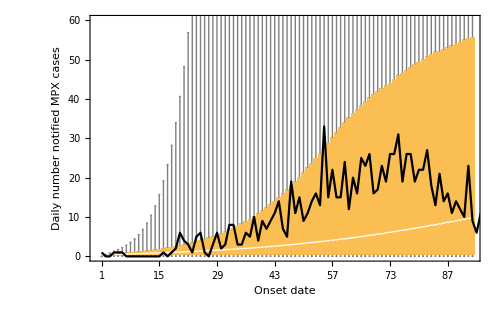

```mathematica
Show[ 
BoxWhiskerChart[Table[Table[nSymp[it][[j]], {j,nsim}],{it,Tmax}],PlotRange->{{0,Tmax},{0,60}},BaseStyle->{FontFamily->"Arial",FontSize->12},
ChartLabels->{"1","","","","","","","8","","","","","","","15","","","","","","","22","","","","","","","29","","","","","","","36","","","","","","","43","","","","","","","50","","","","","","","57","","","","","","","64","","","","","","","73","","","","","","","80","","","","","","","87","","","","","","","94","","","","","","","101"},Frame->{True,True,False,False},FrameLabel->{"Onset date","Daily number notified MPX cases"}],
ListPlot[Table[{it,dataAll[[it]]},{it,1,Length[dataAll]}],PlotStyle->{Black},Joined->True],
ImageSize->500]
```